```mathematica
Needs["PlotLegends`"]
y0 = 1;
xmax = 9;
nmax = 5;
Δx = xmax/nmax;
theTitle = StringForm["Δx = ``", Δx//N];
theX = Table[n Δx, {n,0,nmax}];
theExactSoln = Table[y0 Exp[- n Δx], {n,0, nmax}];
theNumericalSoln =  Table[y0 (1- Δx)^n, {n,0, nmax}];
theImplicitSoln = Table[y0 (1+ Δx)^(-n), {n,0, nmax}];
ListLinePlot[{theExactSoln, theNumericalSoln, theImplicitSoln}, DataRange-> {0,xmax}, PlotLegend-> {"Exact", "Numerical", "Implicit"}, PlotRange-> All, PlotLabel-> theTitle]
```

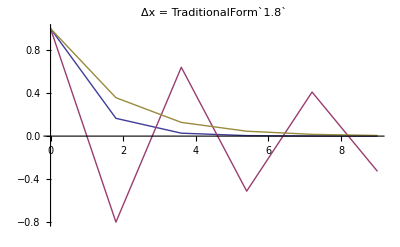

```mathematica
n1max=40
xmax = 8;
δx1 = xmax/n1max//N
δx2 = 4 δx1//N
n2max=n1max/4;
theExactSoln = Table[{n δx1,y0 Exp[- n δx1]}, {n,0, n1max}];
theNumericalSoln =  Table[{n δx1, y0 (1- δx1)^n}, {n,0, n1max}];
theImplicitSoln = Table[{n δx2,y0 (1+ δx2)^(-n)}, {n,0, n2max}];
ListLinePlot[{theExactSoln, theNumericalSoln, theImplicitSoln}, PlotLegend-> {"Exact", "Numerical", "Implicit"}, PlotRange-> All]
```

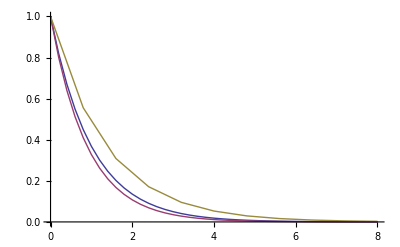

```mathematica
init = {1, 0};
reg = { {1, δt},{-δt, 1}};
impl = Inverse[{ {1, -δt},{δt, 1}}]
implV = {{1-δt^2, δt}, {-δt, 1}};
implX = {{1, δt}, {-δt, 1-δt^2}};
implVX = implV.implX  /. δt->δt/2//Expand
implXV = implX.implV /. δt->δt/2//Expand
funcL = {{reg, "Fwd Euler"}, {impl, "Euler Implicit"}, {implV, "Implicit V"}, {implX,"Implicit X"}, {implXV,"Implicit X∘V" }, {implVX, "Implicit V∘X"}};

AreaTransformation[transM_]:= Module[{dx, dv, new, newx, newv, dA},
new = transM.{x,v};
newx = transM.{x+dx, v}-new;
newv= transM.{x,v+dv}-new;
(* cross product!!!! *)
dA = newx[[1]]newv[[2]]- newx[[2]]newv[[1]]//Expand//Simplify;
Print[StringForm["dA = ``", dA]];
Print[StringForm["Det[transM] = ``", Det[transM]//Simplify]];
]

VisualizeSeries[transformM_,initVec_, numIters_] :=  Module[
{evals,evecs,α, β,  vecTrans, evExpr, matExpr,transName},
{transM, transName}=transformM;
Print[StringForm["Transformation is: ``  (``)", MatrixForm[transM],transName]];
{evals,evecs} = Eigensystem[transM];
vecTrans = Inverse[Transpose[evecs]];
{α, β} = vecTrans.initVec;
evExpr = α (evals[[1]])^numIters evecs[[1]] + β (evals[[2]])^numIters evecs[[2]]//Expand//MatrixForm;
matExpr = MatrixPower[transM, numIters, initVec]//Expand;
Print[StringForm["mat expr: ``", matExpr//MatrixForm]];
Print[StringForm["evals=``, evecs=``", evals, evecs]];
If[matExpr ≠ evExpr,Print[StringForm["ev expr: ``", evExpr]]];
AreaTransformation[transM];
Print[StringForm["============================"]];
]

nStep = 1;
For[ i=1, i≤Length[funcL], i++,
VisualizeSeries[funcL[[i]], {x,v}, 1];
]
```

```mathematica
(*  MUST compare this to symplectic scheme!!!  *)
GenPlots[δt0_, numIters_, plotFunc_, OptionsPattern[{plotMax->1.3, imgSz->100}] ] := Module[{pts, max},
max = OptionValue[plotMax];
Print[StringForm["δt = `` (``), numIters = ``, cycles = ``", δt0, NumberForm[δt0//N, 4], numIters, δt0 numIters/(2 Pi)]];
pts=Table[ Table[MatrixPower[funcL[[k,1]]/.δt->δt0//N ,j, init], {j, 0, numIters}], {k, 1, Length[funcL]}];
Print[Table[plotFunc[pts[[i]] , ImageSize->OptionValue[imgSz],AspectRatio->Automatic, PlotStyle->PointSize[0.005],PlotRange-> {{-max,max}, {-max,max}} , PlotLabel-> funcL[[i,2]]], {i,1,Length[pts]}]]
]

J = 80;
δT = 2 Pi / J ;
For[K=1, K≤6,K++,
GenPlots[K δT, J, ListPlot];
]
GenPlots[0.25, 800, ListLinePlot];
GenPlots[Pi/4, 8, ListLinePlot];
GenPlots[Pi/4, 128, ListPlot];
```

```mathematica
GenPlots[3Pi / 5, 80, ListPlot, plotMax->3, imgSz-> 150];
GenPlots[2Pi / 3, 80, ListPlot, plotMax->100, imgSz-> 150];
```

```mathematica
TransformationProperties[eqnL_] := Module[{},
sol=Solve[eqnL, {x[n+1], v[n+1]}];
f1 = x[n+1]/. sol[[1]];
f2 = v[n+1]/. sol[[1]];
Print[StringForm["f1 = ``, f2 = ``", f1, f2]];
jac = D[{f1, f2}, {{x[n], v[n]}}];
Print[StringForm["Jacobian = ``, Det[Jacobian]=``", jac, Det[jac]]];
Print[StringForm["============================"]];
]

euler = {x[n+1] - x[n] == v[n] δt, v[n+1]- v[n] == -Sin[x[n]] δt};
implicit = {x[n+1] - x[n] == v[n+1] δt, v[n+1]- v[n] == -Sin[x[n+1]] δt};
implicitV = {x[n+1] - x[n] == v[n+1] δt, v[n+1]- v[n] == -Sin[x[n]] δt};
implicitX = {x[n+1] - x[n] == v[n] δt, v[n+1]- v[n] == -Sin[x[n+1]] δt};
implicitVf = {x[n+1] - x[n] == v[n+1] δt, v[n+1]- v[n] == -f[x[n]] δt};
implicitXf = {x[n+1] - x[n] == v[n] δt, v[n+1]- v[n] == -f[x[n+1]] δt};
(*

TransformationProperties[implicit]
*)
TransformationProperties[euler]
TransformationProperties[implicitV]
TransformationProperties[implicitX]
TransformationProperties[implicitVf]
TransformationProperties[implicitXf]
```

```mathematica
(* keep going this way, we will find symplectic transforms for the gyromotion case, somehow *)
```

```mathematica
(* need to invesitagte not just det[Jac] but also Jav J jac^T = I *)
GyroTransformationProperties[eqnL_] := Module[{sol, f1, f2, f3, f4, jac},
sol=Solve[eqnL, {x[n+1], y[n+1], vx[n+1], vy[n+1]}];
f1 = x[n+1]/. sol[[1]]//Expand;
f2 = y[n+1]/. sol[[1]]//Expand;
f3 = vx[n+1]/. sol[[1]];
f4 = vy[n+1]/. sol[[1]];
Print[StringForm["f1 = ``", f1]];
Print[StringForm["f2 = ``", f2]];
Print[StringForm["f3 = ``", f3]];
Print[StringForm["f4 = ``", f4]];
jac = D[{f1, f2, f3, f4}, {{x[n], y[n], vx[n], vy[n]}}];
If[False, Print[StringForm["Jacobian = ``", jac]]];
Print[StringForm["Det[Jacobian]=``", Det[jac]//Simplify]];
Print[StringForm["============================"]];
]

euler = {x[n+1] - x[n] == vx[n] δt, y[n+1] - y[n] == vy[n] δt, 
vx[n+1]- vx[n] == qovm(Ex[x[n],y][n] + vy[n] Bz)δt, vy[n+1]- vy[n] == qovm(Ey[x[n],y[n]] - vx[n] Bz)δt};

implicitV = {x[n+1] - x[n] == vx[n+1] δt, y[n+1] - y[n] == vy[n+1] δt, 
vx[n+1]- vx[n] == qovm(Ex[x[n],y[n]] + vy[n+1] Bz)δt, vy[n+1]- vy[n] == qovm(Ey[x[n],y[n]] - vx[n+1] Bz)δt};

borisV = {x[n+1] - x[n] == vx[n+1] δt, y[n+1] - y[n] == vy[n+1] δt, 
vx[n+1]- vx[n] == qovm(Ex[x[n],y[n]] + 1/2 (vy[n]+ vy[n+1]) Bz)δt, vy[n+1]- vy[n] == qovm(Ey[x[n],y[n]] - 1/2 (vx[n] +vx[n+1])Bz)δt};

GyroTransformationProperties[euler]
GyroTransformationProperties[implicitV]
GyroTransformationProperties[borisV]
```